10 x+3 x^2+y^2

-10 y+2 x y

10+6 x

-10+2 x

(-10+2 x) (10+6 x)-4 y^2

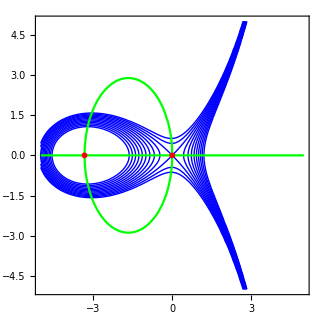

-Graphics3D-

{{x→-10/3,y→0},{x→0,y→0},{x→5,y→-5 ⅈ √5},{x→5,y→5 ⅈ √5}}

-100

500/3

-10

```mathematica
ClearAll["Global`*"];
F[x_,y_]=x^3+5x^2+x*y^2-5y^2;
Fx[x_,y_]=D[F[x,y],x];
Fy[x_,y_]=D[F[x,y],y];
Fxx[x_,y_]=D[Fx[x,y],x];
Fyy[x_,y_]=D[Fy[x,y],y];
Print[Fx[x,y]];
Print[Fy[x,y]];
Print[Fxx[x,y]];
Print[Fyy[x,y]];
test[x_,y_]=Fxx[x,y]*Fyy[x,y]-D[Fx[x,y],y]^2;
Print[test[x,y]];
cpf = ContourPlot[F[x,y],{x,-5,5},{y,-5,5},Contours->{-2,-1,0,1,2,3,4,5,6,7,8,9},ContourStyle->Directive[Blue,Line],ContourShading->None];
cpfx = ContourPlot[{Fx[x,y]==0,Fy[x,y]==0},{x,-5,5},{y,-5,5},ContourStyle->Directive[Green,Line]];
plot=Show[cpf,cpfx,ListPlot[{{0,0},{-10/3,0}},PlotStyle->Red]]
Plot3D[F[x,y],{x,-5,5},{y,-5,5},PlotStyle->None,MeshStyle->Blue]

(*Critical Points occur at Fx=Fy=0:
(0,0),(1,1),((-1)^(1/3),(-1)^(2/3)),((-1)^(2/3),-(-1)^(1/3))
*)
Print[Solve[{Fx[x,y]==0,Fy[x,y]==0},{x,y}]];
Print[test[0,0]];
Print[test[-10/3,0]];
Print[Fxx[-10/3,0]];
```